# Chapter 6 - Problem 3

## Part I. Constants, Given Information and Functions

For this problem, we will need to calculate a few things from the given information, but our constants will pretty much remain the same as before.

```mathematica
Clear["Global`*"];
(* Our PP and PI functions remain unchanged *)
PI[kL_,kR_]= MatrixExp[(1/2) * Log[kL/kR] * ( PauliMatrix[1] - IdentityMatrix[2])];
PP [kx_,l_] = MatrixExp[-I * kx * l * PauliMatrix[3]];
```

Constants and Conversion Factors

```mathematica
h = 6.62607004 * 10^(-34) ;(* planck's constant *)
m = 9.10938 * 10^(-31); (* planck's constant *)
ℏ = h/(2*Pi);
e = 1.60217 * 10 ^(-19); (* 1 electron volt (ev) = e Joules *)
nano = 1 *10^(-9);
alpha = √((2*m*e)/ℏ^2) * nano;
```

The given information

```mathematica
V1 = 2;
V2 = -0.5*V1;
a = 0.15;
b = 0.05;
c = 0.025;
ka = alpha*√(epi - V1);
kb = alpha*√(epi-V2);
kc = alpha*√epi;
numofbarriers = 3; (* this should be renamed number of periods, but to keep consistancy, let's use the same period *)
```

## Part II. The Transfer Matrix

So this system is kind of a weird one. But let’s attempt to find the transfer matrix. B is the area with 0 potential. This will be a pretty long series of PP-PI matrices. However, if we center the “a” block, we notice that both the sides are the same! This means that we can make that into a variable (or a function) so that it will be easier to multiply. Then we can use MatrixPower.

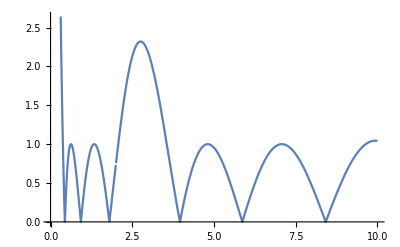

```mathematica
SideProduct1 = PP[kc,c].PI[kc,kb].PP[kb,b].PI[kb,kc].PP[kc,b];
SideProduct2 = PP[kc,b].PI[kc,kb].PP[kb,b].PI[kb,kc].PP[kc,c];
(* Above is the matrices that makes up the PP-PI combination for the side pieces*)
CenterProduct = PI[kc,ka].PP[ka,a].PI[ka,kc];
(* This makes up the "a" piece in the middle *)
TransferMatrix = MatrixPower[SideProduct1.CenterProduct.SideProduct2, numofbarriers];
Subscript[P, 11] = Tr[TransferMatrix]/2;
TransferPlot = Plot[Abs[Subscript[P, 11]],{epi,0,10}]
```

## Part III. The Forbidden bands

So let’s plot the line at 1 again, because we know that anything > 1 will be the forbidden band. Then we can shift our graph to zero to double check (doing it both ways will ensure that you know where your roots are. Don’t forget that you can right click on the graph and find out (approximately) where the roots are so that you can put them into your FidnRoots function.

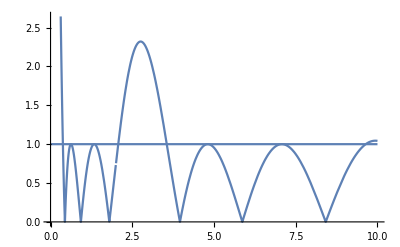

```mathematica
LineAtOne = Plot[1,{epi,0,10}];
Show[TransferPlot, LineAtOne]
```

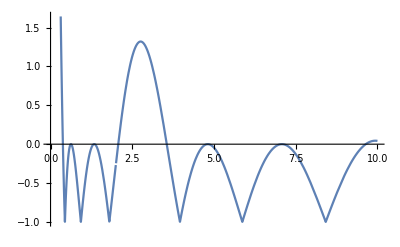

```mathematica
ShiftedTransferPlot = Plot[Abs[Subscript[P, 11]] - 1, {epi,0,10}]
```

So again, we can see that there are about 8 roots that we are are concerned about. Maybe 10, s
o we can check that too, just in case it is within our range of 0 <= epi <= 10 eV.

```mathematica
NumOfRoots = 4;
Array[ForbiddenRoots,NumOfRoots];
Array[StartSearch,NumOfRoots];
StartSearch[1] = 1.8;
StartSearch[2] = 3.5;
StartSearch[3] = 0.58;
StartSearch[4] = 0.63;
(*StartSearch[5] = 2;
StartSearch[6] = 3.5;
StartSearch[7] = 4.7;
StartSearch[8] = 4.8;
StartSearch[9] = 6.9;
StartSearch[10] = 7.1;*)
For[i = 1 , i <=NumOfRoots , i++,
ForbiddenRoots[i]= epi/.FindRoot[Abs[Subscript[P, 11]]== 1,{epi,StartSearch[i]}];]
For[i = 1, i ≤NumOfRoots , i+= 2,
Print["Forbidden band from \n\t", ForbiddenRoots[i], " eV to ", ForbiddenRoots[i+1], " eV"]]
```

Forbidden band from 
	2.07136 eV to 3.55557 eV

Forbidden band from 
	0.62493 eV to 0.62493 eV

NOTE: our answer is going to be the THIRD forbidden band. We ignore the singular values of ϵ because these are not bands. Because FindRoots finds when it equals to 1. We need anything greater than 1. NOT greater than or equal to.
Answer:
Forbidden band is from 2.82949 eV to 4.39106 eV